```mathematica
r[t]=√(-z[t]^2+R^2);
D[r[t],t]
D[r[t],t]^2
```

-(z[t] z'[t])/(√(R^2-z[t]^2))

(z[t]^2 z'[t]^2)/(R^2-z[t]^2)

```mathematica
1+1/(1-R^2/z^2)
```

```mathematica
(1-R^2/z^2+1)/(1-R^2/z^2)
```

(2-R^2/z^2)/(1-R^2/z^2)

```mathematica
Simplify[(2-R^2/z^2)/(1-R^2/z^2)]
```

(R^2-2 z^2)/(R^2-z^2)

```mathematica
Together[1+1/(1-R^2/z^2)]
```

(R^2-2 z^2)/(R^2-z^2)

```mathematica
z^2/(z^2-R^2)+1
```

1+z^2/(-R^2+z^2)

```mathematica
Together[1+z^2/(-R^2+z^2)]
```

(-R^2+2 z^2)/(-R^2+z^2)

```mathematica
Simplify[(-R^2+2 z^2)/(-R^2+z^2)]
```

(R^2-2 z^2)/(R^2-z^2)

```mathematica
z^2/(R^2-z^2)+(R^2-z^2)/(R^2-z^2)//Simplify
```

R^2/(R^2-z^2)

```mathematica
Veff=2k(√(R^2-z^2)-r0)^2-m ω^2(R^2-z^2);
deriv=D[Veff,z]
```

-(4 k z (-r0+√(R^2-z^2)))/(√(R^2-z^2))+2 m z ω^2

```mathematica
(Solve[deriv==0,z]//Simplify)
(Solve[deriv==0,z]//Simplify)/.{ω->1,R->3,r0->1,m->1,k->1}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→0},{z→-(√(4 k^2 (R^2-r0^4)-4 k m R^2 ω^2+m^2 R^2 ω^4))/(√((-2 k+m ω^2)^2))},{z→(√(4 k^2 (R^2-r0^4)-4 k m R^2 ω^2+m^2 R^2 ω^4))/(√((-2 k+m ω^2)^2))}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→0},{z→-√5},{z→√5}}

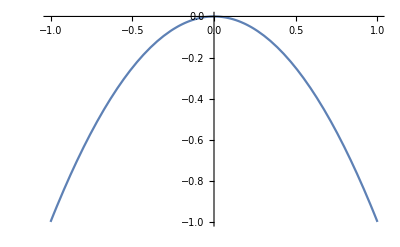

```mathematica
Plot[-x^2,{x,-1,1}]
```

```mathematica
Simplify[-(4 k z (-r0^2+√(R-z^2)))/(√(R-z^2))+2 m z ω^2]
```

2 z (k (-2+(2 r0^2)/(√(R-z^2)))+m ω^2)

```mathematica
Veff/.z->0
```

2 k (√(R^2)-r0^2)^2-m R^2 ω^2

```mathematica
ωc=√((2k)/m(1-r0/R))/.{R->2,r0->1,m->1,k->1};
plot=(Veff/(2k R^2)/.{ω->(α ωc),R->2,r0->1,m->1,k->1})
```

1/8 (2 (-1+√(4-z^2))^2-(4-z^2) α^2)

```mathematica
Manipulate[Plot[{plot/.α->0.4,plot/.α->1.0,plot/.α->a},{z,-2,2}],{a,0,1.0,0.1}]
```

```mathematica
(2 k (-r0+√(R^2-z^2))^2-m (R^2-z^2) ω^2)/(2 k R^2)/.{}
```

(2 k (-r0+√(R^2-z^2))^2-m (R^2-z^2) ω^2)/(2 k R^2)

```mathematica
Clear[r]
```